```mathematica
marketData = SemanticImport[FileNameJoin[{NotebookDirectory[],"logs","market.csv"}]]
```

Dataset[<>]

```mathematica
prices = Normal[marketData[[All,"Price"]]];
```

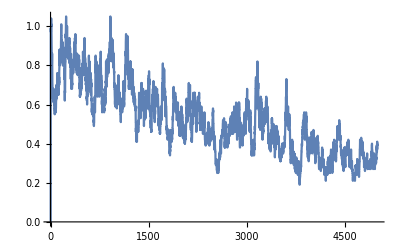

```mathematica
ListLinePlot[prices]
```

```mathematica
Needs["EconomicComputations`"]
```

```mathematica
ret = Returns[DeleteCases[prices,0.]];
```

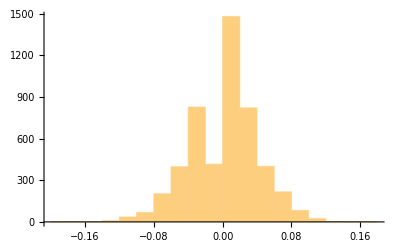

```mathematica
Histogram[ret]
```

```mathematica
tradersData = SemanticImport[FileNameJoin[{NotebookDirectory[],"logs","traders.csv"}]]
```

Dataset[<>]

```mathematica
maWealth = tradersData[Select[StringContainsQ[#TraderName,"ma_trader"~~__]&],{"TraderName","Wealth"}]
```

Dataset[<>]

```mathematica
ziWealth = tradersData[Select[!StringContainsQ[#TraderName,"ma_trader"~~__]&],{"TraderName","Wealth"}]
```

Dataset[<>]

```mathematica
maWealth[Mean,"Wealth"]
```

9.666

```mathematica
ziWealth[Mean,"Wealth"]
```

8.9787

```mathematica
GetPrices[path_String]:=Block[{marketData,prices},
marketData = SemanticImport[FileNameJoin[{NotebookDirectory[],"logs",path,"market.csv"}]];
prices = Normal[marketData[[All,"Price"]]];
Return[DeleteCases[prices,0.]];
];
GetMAWealth[path_String]:=Block[{tradersData,maWealth},
tradersData = SemanticImport[FileNameJoin[{NotebookDirectory[],"logs",path,"traders.csv"}]];
maWealth = tradersData[Select[StringContainsQ[#TraderName,"ma_trader"~~__]&],{"TraderName","Wealth"}];
Return[maWealth];
];
GetZIWealth[path_String]:=Block[{tradersData,ziWealth},
tradersData = SemanticImport[FileNameJoin[{NotebookDirectory[],"logs",path,"traders.csv"}]];
ziWealth = tradersData[Select[!StringContainsQ[#TraderName,"ma_trader"~~__]&],{"TraderName","Wealth"}];
Return[ziWealth];
];
```

```mathematica
directories = FileNames["*",FileNameJoin[{NotebookDirectory[],"logs"}]];
```

```mathematica
nMa = SortBy[Map[FileBaseName,directories],ToExpression]
```

{1,2,3,5,10,20,30,40,50,60,70,80,90}

## Precios

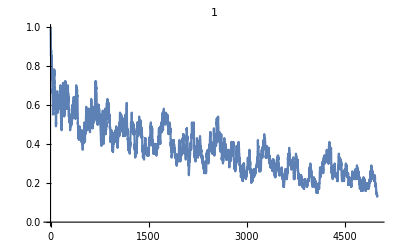
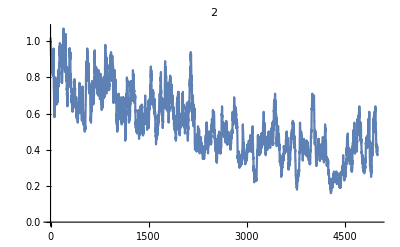
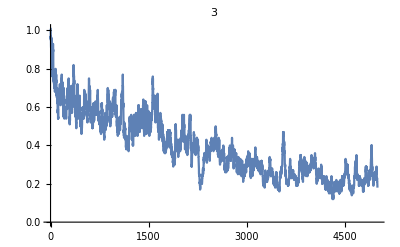
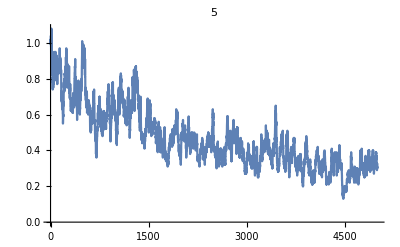
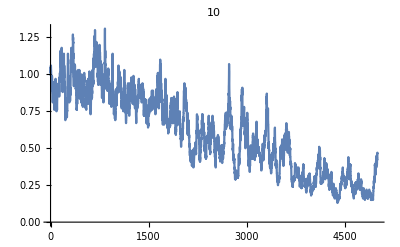
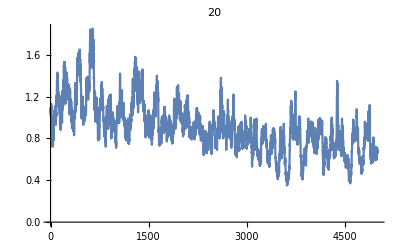
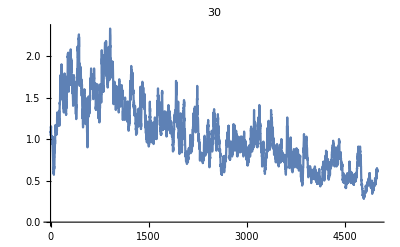
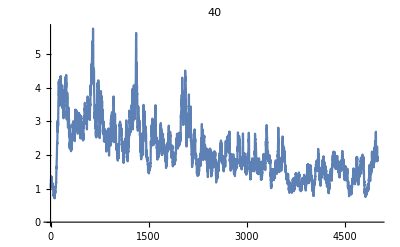

```mathematica
Table[
ListLinePlot[
GetPrices[numberMA],
PlotLabel->numberMA
],
{numberMA,nMa}
]
```

## Retornos

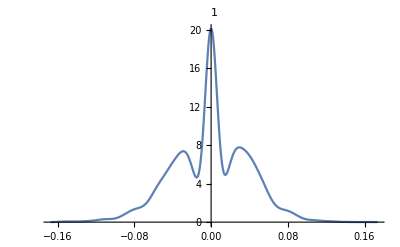
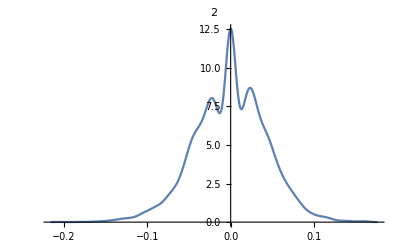
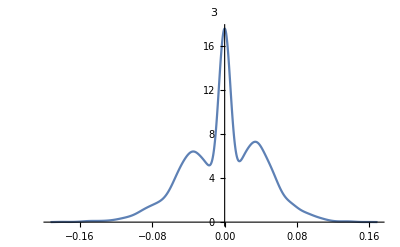
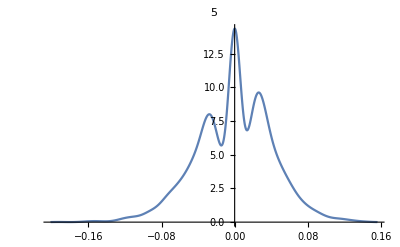
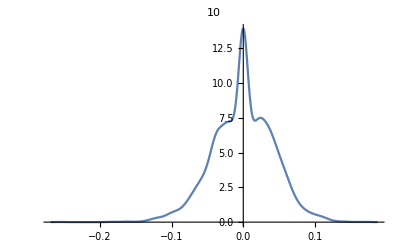
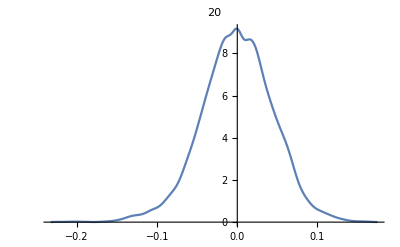
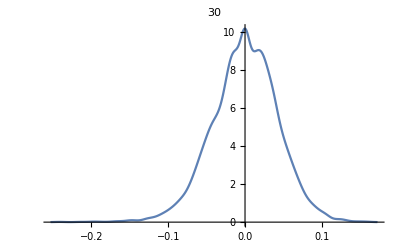
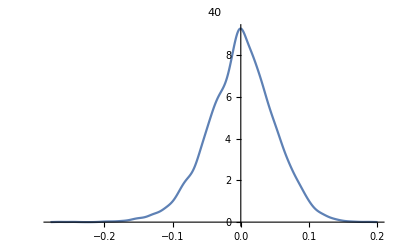

```mathematica
Table[
SmoothHistogram[
Returns[GetPrices[numberMA]],
PlotLabel->numberMA,
PlotRange->All
],
{numberMA,nMa}
]
```

## MA Avg Wealth

```mathematica
maAvg = DeleteCases[
Table[
{ToExpression[numberMA],GetMAWealth[numberMA][Mean,"Wealth"]},
{numberMA,nMa}
],
{_,_Missing}
]
```

{{2,8.63},{3,4.34333},{5,6.544},{10,10.155},{20,14.053},{30,12.7933},{40,34.736},{50,87.2996},{60,107.218},{70,165.352},{80,110.779},{90,113.388}}

## ZI Avg Wealth

```mathematica
ziAvg = Table[
{ToExpression[numberMA],GetZIWealth[numberMA][Mean,"Wealth"]},
{numberMA,nMa}
]
```

{{1,6.5957},{2,9.55398},{3,7.77495},{5,8.98463},{10,9.66833},{20,12.27},{30,10.8116},{40,17.1322},{50,32.0856},{60,45.3433},{70,38.0993},{80,29.604},{90,34.116}}

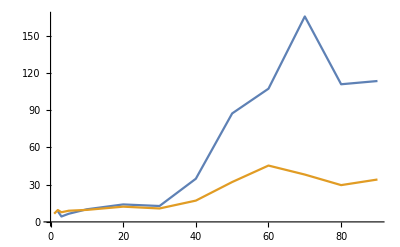

```mathematica
ListLinePlot[{maAvg,ziAvg}]
```

```mathematica
rate = maAvg[[All,2]]/Drop[ziAvg,1][[All,2]]
```

{0.903289,0.558632,0.728355,1.05034,1.14531,1.1833,2.02753,2.72083,2.36459,4.34003,3.74203,3.32359}

```mathematica
numberedRate = Thread[{Map[ToExpression,Drop[nMa,1]],rate}]
```

{{2,0.903289},{3,0.558632},{5,0.728355},{10,1.05034},{20,1.14531},{30,1.1833},{40,2.02753},{50,2.72083},{60,2.36459},{70,4.34003},{80,3.74203},{90,3.32359}}

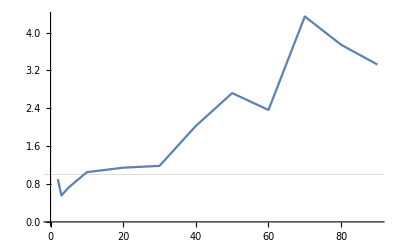

```mathematica
ListLinePlot[numberedRate,GridLines->{{},{1}}]
```